# Central Forces: Homework 4

## John Waczak

1. Legendre Polynomials 

The answers to this problem should have the form of polynomials. For (a) and (b) there should be 5 and for (c) we need to have two polynomial expressions. 


(a) Use Mathematica to find the first 5 Legendre Polynomials

```mathematica
TableForm[Table[{i,TraditionalForm[LegendreP[i,z]]},{i,0,5}], TableHeadings->{None,{"ℓ","P_ℓ(z)"}}]
```

ℓ | P_ℓ(z)
0 | 1
1 | z
2 | 1/2 (3 z^2-1)
3 | 1/2 (5 z^3-3 z)
4 | 1/8 (35 z^4-30 z^2+3)
5 | 1/8 (63 z^5-70 z^3+15 z)

(b) Use Rodgrigues’ formula to calculate the first 5 Legendre polynomials.
Rodrigues’ formula for calculating the “n^th” Legendre polynomial is given by: 
						P_n(z)= 1/(2^n n!)d^n/dx^n[(z^2-1)^n]

```mathematica
TableForm[Table[{i,Simplify[1/(2^i i!)*D[(z^2-1)^i,{z,i}],{i,0,5}]},{i,0,5}], TableHeadings->{None,{"ℓ","P_ℓ(z)"}}]
```

ℓ | P_ℓ(z)
0 | 1
1 | z
2 | 1/2 (-1+3 z^2)
3 | 1/2 z (-3+5 z^2)
4 | 1/8 (3-30 z^2+35 z^4)
5 | 1/8 z (15-70 z^2+63 z^4)

So clearly using the Rodriguez formula as shown above produces the correct Legendre Polynomials. 

(c) See attached pages 

3. Use your favorite tool to generate the Legendre polynomial expansion to the function f(z)=sin(πz). How many terms do you need to to include to get a good approximation to f(z) for -1<z<1? What about the interval -2<z<2. Repeat for g(z)=sin(3πz). 

To answer this question I need to create polynomials and then show how they fit the given functions. I will do this graphically. 


To analyze this problem I will use code from “Legendre Polynomial Series” notebook by Prof. Corinne Manogue (used in class)

```mathematica
f = Sin[Pi*z]
```

```mathematica
lmax:=12
Do[c[m]=Integrate[((2*m+1)/2)*f*LegendreP[m,z],{z,-1,1}],{m,0,lmax}]
```

```mathematica
r = Sum[c[m]*LegendreP[m,z],{m,0,lmax}]
Plot[{r,f},{z,-2,2}]
```

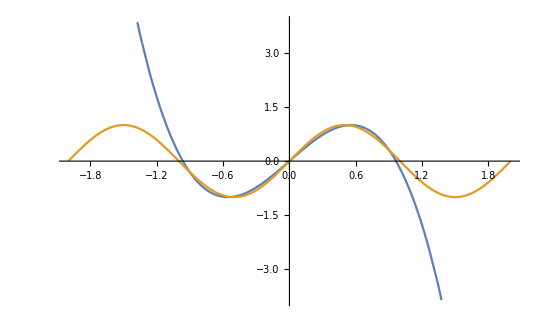
For lmax = 4 we have a very good approximation for f(x) on [-1,1] however this approximation quickly falls apart after this range. 
-Graphics-
For lmax > 4 the approximation becomes better and better. Below is a graph for lmax = 12 which very nearly fits f(x) on [-2,2]

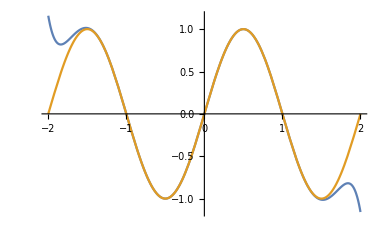

When we try to fit g(z)=sin(3πz) I am expecting to need more terms as g(z) ‘squiggles’ more on [-1,1] than f(z) so we will need higher orders of z.

```mathematica
g=Sin[3*Pi*z]
```

```mathematica
lmax:=24
Do[c[m]=Integrate[((2*m+1)/2)*g*LegendreP[m,z],{z,-1,1}],{m,0,lmax}]
```

```mathematica
r = Sum[c[m]*LegendreP[m,z],{m,0,lmax}]
Plot[{r,g},{z,-2,2}]
```

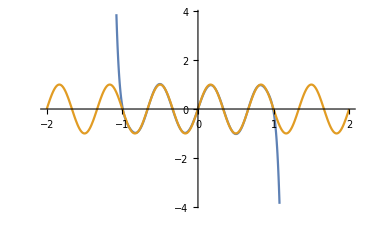
As we can see, using the same terms as our approximation of f to [-2,2] gives a good approximation of g to [-1,1] but nothing more. If we want the solution to converge for [-1,1] which it may not, we need to try higher orders of z by increasing lmax. 
-Graphics-

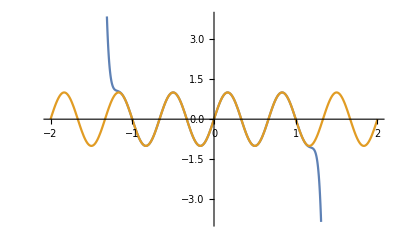
The graph below shows the graph for lmax = 24: 
-Graphics-

Clearly, increasing lmax is having little effect on the behavior outside of the [-1,1] and so, as was mentioned in class, we can see why the Legendre polynomials only have guaranteed convergence on [-1,1]

6. (a) Graph the Yukawa potential with and without the experimental term. Describe how it approximates the ‘real’ situation. In particular, describe the role of alpha. 

To solve this problem I will produce graphs for the various cases above and comment on the effect of the parameter alpha.

```mathematica
k = 1 
α = 1
Uy[r_]:= -k/r*ⅇ^(-r/α)
Plot[{Uy[r], -k/r},{r,0,10}, PlotLegends->"Expressions"]
```

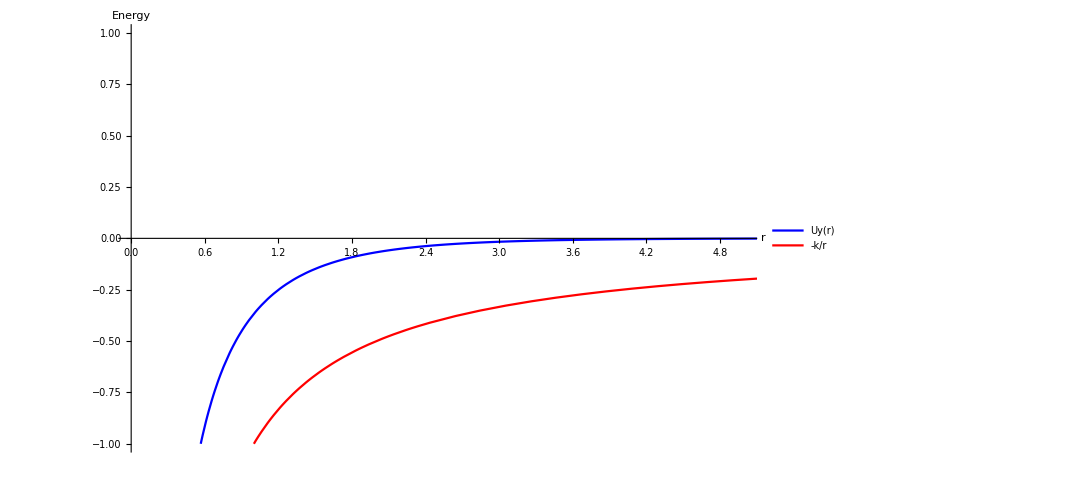

As the above graph shows, the value alpha separates the Yukawa potential from the -1/r potential. In the limit as α →∞, the Yukawa potential approaches the -1/r potential. So the Yukawa is ‘screened’ from the Coulomb potential by α. 

(b). Draw the effective potential for the two choices α=10 and α=0.1 with k=1 and ℓ=1. 

To solve this problem I need to make two graphs for the parameters specified above. I will assume μ=1 for the effective potential as this was not specified but is another required parameter.

1

10

0.1

1

1

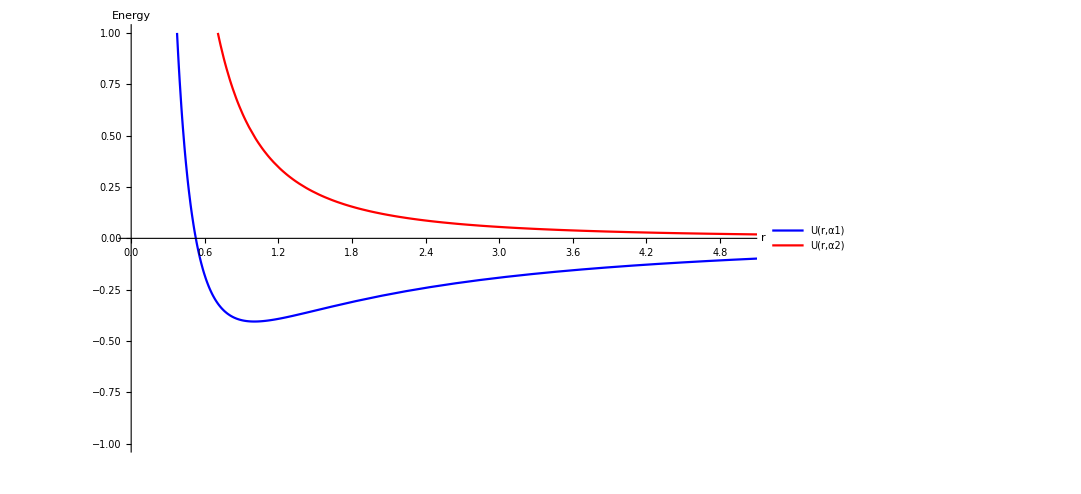

```mathematica
k = 1 
α1 = 10
α2 = 0.1
ℓ = 1 
μ = 1

U[r_, α_]:=ℓ^2/(2*μ*r^2) -k/r*ⅇ^(-r/α)
Plot[{U[r,α1], U[r,α2]},{r,0,10}, PlotLegends->"Expressions"]
```

The above graph demonstrates how for small α, Ueff does not change concavity. It appears that so long as α > 1 we see the dip required for stable circular orbits. This dip is required because without it you can not define a minimum Ueff for which we would see circular orbits.